```mathematica
(*Define the functions for x,y,and z*)x[u_,v_]:=(Sqrt[2]-u-v/Sqrt[3])/Sqrt[2]
y[u_,v_]:=1-x[u,v]-Sqrt[2]*v/Sqrt[3]
z[u_,v_]:=2*v/Sqrt[6]

(*Define the entropy function*)
H[x_,y_,z_]:=-x*Log2[x]-y*Log2[y]-z*Log2[z]

(*Define the conditions for u and v*)
cond1[u_,v_]:=u>=0&&u<=1/Sqrt[2]&&v<=Sqrt[3]*u
cond2[u_,v_]:=u>1/Sqrt[2]&&u<=Sqrt[2]&&v<=Sqrt[6]-Sqrt[3]*u

(*Generate the plot*)
plot=ParametricPlot3D[{u,v,H[x[u,v],y[u,v],z[u,v]]},{u,0,Sqrt[2]},{v,0,Sqrt[6]},RegionFunction->Function[{u,v},cond1[u,v]||cond2[u,v]],PlotPoints->60,BoxRatios->{1,1,1},ColorFunction->"Rainbow",Mesh->{50,50},MeshFunctions->{#4&,#5&}]

(*Display the plot*)
Show[plot]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Define the functions for x,y,and z*)x[u_,v_]:=(Sqrt[2]-u-v/Sqrt[3])/Sqrt[2]
y[u_,v_]:=1-x[u,v]-Sqrt[2]*v/Sqrt[3]
z[u_,v_]:=2*v/Sqrt[6]

(*Define the entropy function*)
H[x_,y_,z_]:=-x*Log2[x]-y*Log2[y]-z*Log2[z]

(*Define the conditions for u and v*)
cond1[u_,v_]:=u>=0&&u<=1/Sqrt[2]&&v<=Sqrt[3]*u
cond2[u_,v_]:=u>1/Sqrt[2]&&u<=Sqrt[2]&&v<=Sqrt[6]-Sqrt[3]*u

(*Generate the plot*)
plot=ParametricPlot3D[{u,v,H[x[u,v],y[u,v],z[u,v]]},{u,0,Sqrt[2]},{v,0,Sqrt[6]},RegionFunction->Function[{u,v,w},cond1[u,v]||cond2[u,v]],PlotPoints->150,BoxRatios->{1,1,1},ColorFunction->"Rainbow",Mesh->{50,50},MeshFunctions->{#4&,#5&}, PlotStyle->Thickness[0.005]]

(*Export to STL for 3D printing*)
Export["entropy_function.stl",DiscretizeGraphics[plot]]
```

-Graphics3D-

entropy_function.stl

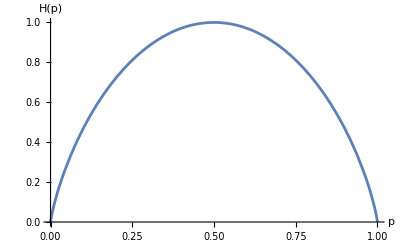

-Graphics-

```mathematica
(*Define the entropy function*)H[p_]:=-p*Log2[p]-(1-p)*Log2[1-p]

(*Generate the plot*)
plot=Plot[H[p],{p,0,1},PlotRange->All,AxesLabel->{"p","H(p)"}]

(*Display the plot*)
Show[plot]
```

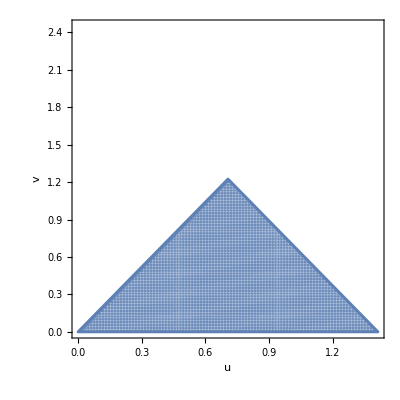

-Graphics-

```mathematica
(*Generate the plot*)plot=RegionPlot[cond1[u,v]||cond2[u,v],{u,0,Sqrt[2]},{v,0,Sqrt[6]},PlotPoints->200,AxesLabel->{"u","v"}]

(*Display the plot*)
Show[plot]
```

{{0,0},{√2,0},{1/(√2),√(3/2)}}

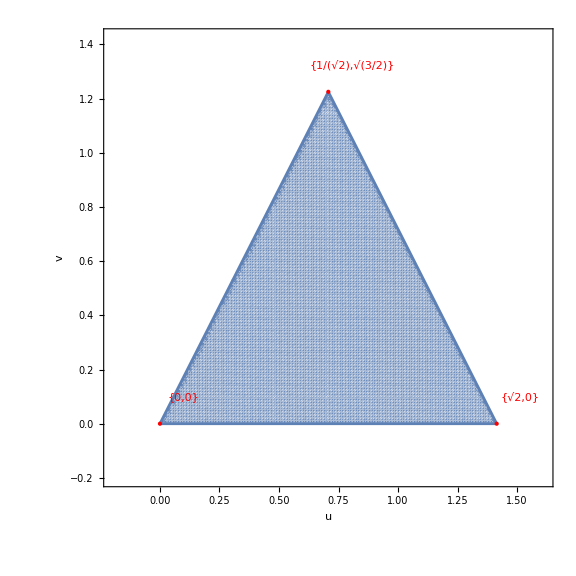

-Graphics-

```mathematica
(*Define the conditions for u and v*)cond1[u_,v_]:=u>=0&&u<=1/Sqrt[2]&&v<=Sqrt[3]*u && v>= 0
cond2[u_,v_]:=u>1/Sqrt[2]&&u<=Sqrt[2]&&v<=Sqrt[6]-Sqrt[3]*u && v>= 0

(*Define the corner points*)
points={{0,0},{Sqrt[2],0},{1/Sqrt[2],Sqrt[6]/2}}

(*Generate the plot*)
plot=RegionPlot[cond1[u,v]||cond2[u,v],{u,-0.4,Sqrt[2]+0.4},{v,-0.4,Sqrt[6]/2+0.4},PlotPoints->200,AxesLabel->{"u","v"},AspectRatio->1,PlotRange->{{-0.2,Sqrt[2]+0.2},{-0.2,0.2+Sqrt[6]/2}},Epilog->{Red,PointSize[Large],Point[points],Map[Text[#,#+0.1]&,points]}]

(*Display the plot*)
Show[plot]
```

{{0,0},{√2,0},{1/(√2),√(3/2)}}

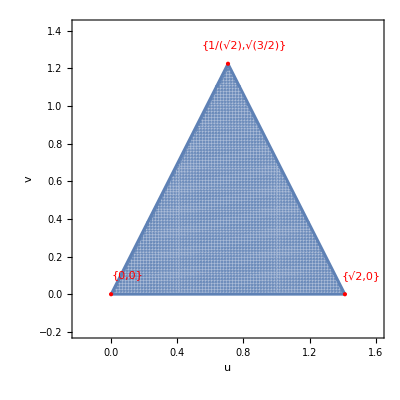

-Graphics-

```mathematica
(*Define the conditions for u and v*)cond1[u_,v_]:=u>=0&&u<=1/Sqrt[2]&&v<=Sqrt[3]*u&&v>=0
cond2[u_,v_]:=u>1/Sqrt[2]&&u<=Sqrt[2]&&v<=Sqrt[6]-Sqrt[3]*u&&v>=0

(*Define the corner points*)
points={{0,0},{Sqrt[2],0},{1/Sqrt[2],Sqrt[6]/2}}

(*Generate the plot*)
plot=RegionPlot[cond1[u,v]||cond2[u,v],{u,-0.2,Sqrt[2]+0.2},{v,-0.2,0.2+Sqrt[6]/2},PlotPoints->200,AxesLabel->{"u","v"},AspectRatio->1,PlotRange->{{-0.2,Sqrt[2]+0.2},{-0.2,0.2+Sqrt[6]/2}},Epilog->{Red,PointSize[Large],Point[points],Map[Text[#,#+0.1]&,points]}]

(*Display the plot*)
Show[plot]
```

```mathematica
(*Define the functions for x,y,and z*)x[u_,v_]:=(Sqrt[2]-u-v/Sqrt[3])/Sqrt[2]
y[u_,v_]:=1-x[u,v]-Sqrt[2]*v/Sqrt[3]
z[u_,v_]:=2*v/Sqrt[6]

(*Define the entropy function*)
H[x_,y_,z_]:=-x*Log2[x]-y*Log2[y]-z*Log2[z]

(*Define the conditions for u and v*)
cond1[u_,v_]:=u>=0&&u<=1/Sqrt[2]&&v<=Sqrt[3]*u&&v>=0
cond2[u_,v_]:=u>1/Sqrt[2]&&u<=Sqrt[2]&&v<=Sqrt[6]-Sqrt[3]*u&&v>=0

(*Generate the entropy function plot*)
entropyPlot=ParametricPlot3D[{u,v,H[x[u,v],y[u,v],z[u,v]]},{u,0,Sqrt[2]},{v,0,Sqrt[6]},RegionFunction->Function[{u,v,w},cond1[u,v]||cond2[u,v]],PlotPoints->150,BoxRatios->{1,1,1},ColorFunction->"Rainbow",Mesh->{50,50},MeshFunctions->{#4&,#5&},PlotStyle->Thickness[0.01]] ;

(*Generate the base plot*)
basePlot=ParametricPlot3D[{u,v,0},{u,-0.2,Sqrt[2]+0.2},{v,-0.2,0.2+Sqrt[6]/2},RegionFunction->Function[{u,v,w},cond1[u,v]||cond2[u,v]],PlotPoints->200,BoxRatios->{1,1,0.2},PlotRange->{{-0.2,Sqrt[2]+0.2},{-0.2,0.2+Sqrt[6]/2},{0,0.2}}, PlotStyle->Thickness[0.03]];

(*Combine the plots*)
combinedPlot=Show[entropyPlot,basePlot]

(*Export to STL for 3D printing*)
(*Export the entropy function plot*)Export["entropy_plot.stl",DiscretizeGraphics[entropyPlot]]

(*Export the base plot*)
Export["base_plot.stl",DiscretizeGraphics[basePlot]]
```

-Graphics3D-

entropy_plot.stl

base_plot.stl

```mathematica
(*Define the conditions for u and v*)cond1[u_,v_]:=u>=0&&u<=1/Sqrt[2]&&v<=Sqrt[3]*u&&v>=0
cond2[u_,v_]:=u>1/Sqrt[2]&&u<=Sqrt[2]&&v<=Sqrt[6]-Sqrt[3]*u&&v>=0

(*Generate the base plot with a small thickness*)
basePlot=Show[ParametricPlot3D[{u,v,0},{u,-0.2,Sqrt[2]+0.2},{v,-0.2,0.2+Sqrt[6]/2},RegionFunction->Function[{u,v,w},cond1[u,v]||cond2[u,v]],PlotPoints->200,BoxRatios->{1,1,0.2},PlotRange->{{-0.2,Sqrt[2]+0.2},{-0.2,0.2+Sqrt[6]/2},{0,0.2}}],ParametricPlot3D[{u,v,0.01},{u,-0.2,Sqrt[2]+0.2},{v,-0.2,0.2+Sqrt[6]/2},RegionFunction->Function[{u,v,w},cond1[u,v]||cond2[u,v]],PlotPoints->200,BoxRatios->{1,1,0.2},PlotRange->{{-0.2,Sqrt[2]+0.2},{-0.2,0.2+Sqrt[6]/2},{0,0.2}}]]

(*Export the base plot*)
Export["base_plot.stl",DiscretizeGraphics[basePlot]]
```

-Graphics3D-

base_plot.stl